```mathematica
BeginPackage["MeFuncs`"];

xH={1,0};
yH={0,1};
rH={Cos[#],Sin[#]}&;

$PrePrint=StandardForm;
(*Begin["`Private`"]*)
CsQ:=DeleteElements[#[[1]]*#[[2]],{0}]&[{#,Flatten[Attributes[#]/.{Constant->1,{}->{0}}]}]&[Vars[#]]&
Flatn:=DeleteElements[#[[2]],#[[1]]]&[Flatten/@{{List@@({##}/.#1->{Null})},#1}]&
FNCheck:=Module[{},Print[{#1,#2,#3}];Print[Defer[#2[#1]==#3[#1]]];#2[#1]==#3[#1]]&
Intg:=Extract[#,Flatn[{Position[#,Integrate]},0]][[1]]&[FullForm[#]]&
Intl:=Extract[#,Flatn[{Position[#,Integrate]},0]][[2]]&[FullForm[#]]&
Mag:=If[VectorQ[#],Sqrt[#.#],#]&;
RP:=If[ContainsAny[{0,Null},##],#[[2]],#[[2]]//.Thread[#[[3]]->#[[4]]],MaxIterations->5]&[{(Times@@Flatten[{##}/.Thread[{#1,#2,#3}->{1,1,1}]]),#1,#2,#3}]&
RPT:=Express_:>Module[{},
(Express/.If[!ContainsAny[{0,Null,{}},{##}],Thread[#2->#3],Thread[#3->#3]])&[Times@@Flatten[{##}/.{#1->1,#2->1}],#1,#2]
]&
SS:=#[[1]]/.Solve[#[[2]]==0,#[[1]]][[If[#[[3]]===Null,1,#[[3]]]]]&[{#1,#2,Times@@({##}/.Thread[{#1,#2}->{1,1}])}]&
S:=If[#2===3,#1/.g21[],#1]&[If[AnyMatch[{2,3},#2],TrigReduce[#1],#1],#2]&[If[AnyMatch[{0,Null},#2],#1,
Refine[FullSimplify[#1],Variables[#1]∈Reals]/.Abs[q_]:>q],#2]&[#1,(Times@@({##}/.#1->1))]&;

g20:=Express_:>Module[{},
Express/.Thread[#2[[2]]*#2[[1]]->ConstantArray[0,Length[#2[[1]]]]]&[Express,##]&[If[##===Null,
{{},1},
If[ContainsAny[{Null},{##}],
{{##}[[1]],0},
{{##}[[1]],1}]]]]&
g21:=Express_:>Module[{},
Express/.Thread[#2[[2]]*Join[#2[[1]],#3[[1]]]->#2[[2]]*ConstantArray[1,Length[Join[#2[[1]],#3[[1]]]]]]&[##,{DeleteCases[(Boole[MemberQ[Attributes[#],Constant]&/@Vars[#1]])*(#&/@Vars[#1]),0],Vars[#1]}]&[Express,##]&[If[##===Null,
{{},1},
If[ContainsAny[{Null},{##}],
{{##}[[1]],0},
{{##}[[1]],1}]]]]&

Trm:=If[Head[Expand[#]]===Plus,List@@Expand[#],{#}]&;
Vars:=If[AnyMatch[{0,Null},#2],(DeleteCases[Dt/@#1,0]/.HoldPattern[Dt[q_]]:>q),#1]&[Variables[#1//.{f_[q_]|Exp[q_]:>q}],#2]&[(If[Head[Trm[#1][[1]]]===Power,(Trm[#1][[1,1]]),Trm[#1]]),(Times@@Flatten[{##}/.#1->1])]&
(*!FreeQ[#,Integrate]*)
QA:=Table[#1,{#2,#3}]&[#1,If[AnyMatch[{1,Null},#1],i,Vars[#1][[1]]],#2]&;

d:=Nest[Dt,#1,(Times@@{##}/.#1->1)]//.HoldPattern[Dt[q_Symbol]]->Derivative[1][q]&
Format[Derivative[n_][f_]]=OverDot[f,n];

PRM[param_:t,unParam_:0]:=Express_:>Module[{Terms,vars,args,maps},
Catch[
Terms=If[Head[Expand[#]]===Plus,List@@Expand[#],{#}]&[Express/.g21[]];
vars=Variables[Terms];
If[!unParam==0,Throw[Express/.(q_[param]->q&)/@vars]];
args=Vars[vars];
maps=Table[If[!MatchQ[vars[[i]],Derivative[n_][f_][param]|Derivative[n_][f_]],
vars[[i]]/.(#->#[param]&)/@args,
If[MatchQ[vars[[i]],Derivative[n_][f_]],
vars[[i]]/.Derivative[n_][f_]->Derivative[n][f][param],
vars[[i]]
]
],
{i,Length[vars]}];
Express/.Thread[vars->maps]
]
];

(*End[]*)
EndPackage[]
```

```mathematica
Quit
```

```mathematica
ClearAll["Global`*"]
SetAttributes[{h,M,M2,m,g},Constant]
$Assumptions=t>=0&&t0>=0&&tf>=0&&h>0&&M>0&&M2>0&&m>0&&g>0;
```

```mathematica
SetAttributes[IntTricks,HoldAll];
(*Calling IntTricks[[2,2,2,2,1]] gives the first replacement rule*)
IntTricks=Integrate[expr_,{t,t0_,tf_}]:>
Module[{Terms,Tricks,Integrals,FnDecoder,InverseSubs,Result},
Terms=If[Head[expr]===Plus,List@@TrigReduce[expr],{TrigReduce[expr]}];

Tricks={(*Order matters here. Terms will go to first match => Complex to simple listing chosen*)
f1_[c1_.t]*f2_[c2_.*q_[t]]*q_'[t]:>f1[c1*t]*Integrate[f2[c2*q],{q,q[t0],q[tf]}],
f_[c1_.*q_[t]]*q_'[t]:>Integrate[f[c1*q],{q,q[t0],q[tf]}],
f_[c1_.*q1_[t]]*q2_'[t]:>f[c1*q1[t]]*Integrate[1,{q2,q2[t0],q2[tf]}],
f1_[c1_.*q1_[t]]*f2_[c2_.*q2_[t]]*q2_'[t]:>f1[c1*q1[t]]*Integrate[f2[c2*q2],{q2,q2[t0],q2[tf]}],
f_[t]:>Integrate[f[t],{t,t0,tf}],

q1_[t]*q2_[t]*q1_'[t]:>q2[t]*Integrate[q1[t],{q1,q1[0],q1[f]}],
q_[t]*q_'[t]:>Integrate[q[t],{q,q[0],q[f]}],
(q1_[t])^c1_.*q2_'[t]:>(q1[t])^c1*Integrate[1,{q2,q2[0],q2[f]}],
q_'[t]:>Integrate[1,{q,q[0],q[f]}]
};

	Integrals=Terms/.Tricks;
Result=Plus@@Integrals/.{t0->0,tf->t}(*/.InverseSubs*)
];/;FreeQ[expr,Integrate];

V2D[Integrand_]:=-Integrate[Integrand,{t,t0,tf}];

ELeq[T_,V_,qs_,Cons_,ShowBool_:0]:=
Module[{L,λs,ELUnCons,ConsQ,ELCons,EqnsUnCon,EqnsCon,Show},
		L=T-V;

	ELUnCons[Lag_,var_]:=D[D[Lag,D[var,t]],t]-D[Lag,var];
	EqnsUnCon=Table[ELUnCons[L,qs[[i]]],{i,Length[qs]}];
If[Length[Cons]==0,
EqnsCon={};,

	λs=Symbol/@("λ"<>ToString[#]&/@Range[Length[Cons]]);
ELCons[UnkMult_,Constraint_,var_]:=UnkMult*D[Constraint,var];
EqnsCon=Table[ELCons[λs[[i]],Cons[[i]],qs[[j]]],{i,1,Length[Cons]},{j,1,Length[qs]}];
];

Show=If[ShowBool==1,
Print[L];
Print[TableForm[EqnsUnCon-Total[EqnsCon],
TableHeadings->{qs,None},TableSpacing->{1,5}]];
If[Length[Cons]>0,
Print[TableForm[Flatten[EqnsCon],
TableHeadings->{Tuples[{λs,qs}],None},TableSpacing->{1,5}]];
]
];
Return[Join[EqnsUnCon-Total[EqnsCon],EqnsCon]]
]
```

```mathematica
C2P=RP[#,{x,y},{r*Cos[a],r*Sin[a]},1]&; (*Use like C2P@{x,y}*)
P2C=RP[#,{r,Cos[a],Sin[a]},{Sqrt[x^2+y^2],x/Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]}]&;
```

```mathematica
TC[x_,y_]=m/2(d[x]^2+d[y]^2);TC[t_]=TC[x,y]/.PRM[]
TP[r_,a_]=m/2(d[r*Cos[a]]^2+d[r*Sin[a]]^2);TP[t_]=TP[r,a]/.PRM[]

	Ipill[r]=RP[Integrate[(M2/r)r'^2,{r',0,r}],{r,M2},{2*h/3,2/3*M}];
TP[a_]=1/2Ipill[r]*d[a]^2;TP[t_]=TP[a]/.PRM[]
```

1/2 m ((ẋ[t])^2+(ẏ[t])^2)

1/2 m ((-r[t] Sin[a[t]] ȧ[t]+Cos[a[t]] ṙ[t])^2+(Cos[a[t]] r[t] ȧ[t]+Sin[a[t]] ṙ[t])^2)

4/81 h^2 M (ȧ[t])^2

```mathematica
Tg[a_]=S[C2P@Cross[{x,y,0},m*g{0,-Sin[π/2-a],0}]]
```

{0,0,-g m r Cos[a]^2}

```mathematica
Fg[a_]=RP[M2*g*Cos[a]{Sin[a],-Cos[a]},{r,M2},{2*h/3,2/3*M}](*FN[a_]=m*g*Sin[a]*{Cos[a],Sin[a]};*)(*F[a_]=Fg+FN[a]*)
```

{2/3 g M Cos[a] Sin[a],-2/3 g M Cos[a]^2}

```mathematica
TestV[a_]=Integrate[Fg[ap],{ap,π/2,a}]
TestP[a_]=Integrate[TestV[ap],{ap,π/2,a}]
```

{-1/3 g M Cos[a]^2,-1/6 g M (2 a-π+Sin[2 a])}

{-1/12 g M (2 a-π+Sin[2 a]),1/24 g M (2-(-2 a+π)^2+2 Cos[2 a])}

```mathematica
Plot[{Fg[a]/.g21[],TestP[a]/.g21[]},{a,π/2,0},ScalingFunctions->{"Reverse",Identity}];
ParametricPlot[{{Fg[a]/.g21[]},{TestP[a]/.g21[]}},{a,π/2,0},AxesLabel->{"x","y"},AspectRatio->1];
```

```mathematica
lC[x_,y_]:={x,y}; lP[r_,a_]:={r*Cos[a],r*Sin[a]};
dlC[x_,y_]:=d[lC[x,y]];dlP[r_,a_]:=RP[d[lP[r,a]],{r,r'},{2h/3,0}];
dlC[x,y];
dlP[r,a];
Vintgs={S[(P2C/@Fg[a]).dlC[x,y]]/.PRM[t],S[Fg[a].dlP[r,a]]/.PRM[t]}/.RPT[{x^2+y^2,x[t]^2+y[t]^2},{2h/3,2h/3}]
VCint[t_]=Vintgs[[1]];VPint[t_]=Vintgs[[2]];
```

{(g M x[t] (y[t] ẋ[t]-x[t] ẏ[t]))/h,-4/9 g h M Cos[a[t]] ȧ[t]}

```mathematica
Vs=RP[{V2D[VCint[t]]/.IntTricks,V2D[VPint[t]]/.IntTricks},{},{}]
VC[t_]=Vs[[1]];VP[t_]=Vs[[2]];
```

{-(-g M x[t]^2 (-y[0]+y[f])+g M (-x[0]+x[f]) x[t] y[t])/h,4/9 g h M (-Sin[a[0]]+Sin[a[t]])}

```mathematica
LC[t_]:=RP[TC[t]-VC[t],{r[t],r'[t]},{R,0},0];LP[t_]:=RP[TP[t]-S[VP[t],2],{r[t],r'[t]},{R,0},0];
LC[x_,y_]:=RP[TC[x,y]-(VC[t]/.PRM[t,1]),{r[t],r'[t]},{R,0},0];LC[x,y];
LP[r_,a_]:=RP[TP[a]-(VP[t]/.PRM[t,1]),{r[t],r'[t]},{R,0},0];LP[r,a];
LC[t]
LP[t]
```

(-g M x[t]^2 (-y[0]+y[f])+g M (-x[0]+x[f]) x[t] y[t])/h+1/2 m ((ẋ[t])^2+(ẏ[t])^2)

4/9 (g h M Sin[a[0]]-g h M Sin[a[t]])+4/81 h^2 M (ȧ[t])^2

```mathematica
Conx[t_]:=x[t]^2+y[t]^2-R^2/.RPT[{R},{(2h/3)}]
Cony[t_]:=x[t]^2+y[t]^2-R^2/.RPT[{R},{(2h/3)}]
ELegsC[t_]=ELeq[TC[t],VC[t],{x[t],y[t]},{Conx[t],Cony[t]},1];
```

(-g M x[t]^2 (-y[0]+y[f])+g M (-x[0]+x[f]) x[t] y[t])/h+1/2 m ((ẋ[t])^2+(ẏ[t])^2)

x[t] | -2 λ1 x[t]-2 λ2 x[t]-(-2 g M x[t] (-y[0]+y[f])+g M (-x[0]+x[f]) y[t])/h+m ẍ[t]
y[t] | -(g M (-x[0]+x[f]) x[t])/h-2 λ1 y[t]-2 λ2 y[t]+m ÿ[t]

{λ1,x[t]} | 2 λ1 x[t]
{λ1,y[t]} | 2 λ1 y[t]
{λ2,x[t]} | 2 λ2 x[t]
{λ2,y[t]} | 2 λ2 y[t]

```mathematica
Conr[t_]:=r[t]-R/.RPT[{R},{2h/3}];
(*Cona[t_]=S[Mag[Fg*Sin[a[t]]-(FN[a]/.PRM[])]-m*r[t]*a'[t]^2]*)
Cona[t_]:=Fg[t].xH
ELegsP[t_]=ELeq[S[TP[t]],S[VP[t]],{r[t],a[t]},{Conr[t],Cona[t]},1];
```

-4/9 g h M (-Sin[a[0]]+Sin[a[t]])+4/81 h^2 M (ȧ[t])^2

r[t] | -λ1
a[t] | 4/9 g h M Cos[a[t]]+8/81 h^2 M ä[t]

{λ1,r[t]} | λ1
{λ1,a[t]} | 0
{λ2,r[t]} | 0
{λ2,a[t]} | 0

```mathematica
ErT[t_]=ELeq[S[TP[t]],VP[t],{r[t],a[t]},{Conr[t],Cona[t]}][[1]]/.Thread[{λ1,λ2}->{0,0}];
EaT[t_]=ELeq[S[TP[t]],VP[t],{r[t],a[t]},{Conr[t],Cona[t]}][[2]]/.Thread[{λ1,λ2}->{0,0}];
EPtotT[t_]=S[ErT[t]+EaT[t],0];
```

```mathematica
EPs=RP[{{S[ErT[t]/.PRM[t,1]]},{S[EaT[t]/.PRM[t,1]]},{S[EPtotT[t]/.PRM[t,1]]}},{r[t],r[0]},{2h/3,2h/3}]
Er=EPs[[1,1]];Ea=EPs[[2,1]];EPtot=EPs[[3,1]];

EPCs={{#[[3,1]],#[[3,2]]},{#[[4,1]],#[[4,2]]}}&[S[RP[ELeq[TP[t],VP[t],{r[t],a[t]},{Conr[t],Cona[t]}],{λ1,λ2},{0,0},1],1]]/.PRM[t,1];
```

{{0},{4/81 h M (9 g Cos[a]+2 h ä)},{4/81 h M (9 g Cos[a]+2 h ä)}}

```mathematica
SS[a'',Ea]
```

-(9 g Cos[a])/(2 h)

```mathematica
Integrate[SS[a'',Ea],{a,a[0],af}]
```

-(9 g (Sin[af]-Sin[a[0]]))/(2 h)

```mathematica
ErSols=SS[a',EPs0[[1,1]]]
EaSols=RP[S[SS[a'',EPs0[[2,1]]]],{r,r[0]},{2h/3,2h/3}]
```

Part::partd: Part specification EPs0⟦1,1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ȧ/.{}⟦1⟧

Part::partd: Part specification EPs0⟦2,1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ä/.{}⟦1⟧

```mathematica
RP[S[RP[Ea,{a'},{ErSols[[1]]}]],{r',r''},{0,0}]
SS[a'',%]
```

m r (g Cos[a]+r ä)

-(g Cos[a])/r

```mathematica
EPs=RP[RP[{{S[ErT[t]/.PRM[t,1]]},{S[EaT[t]/.PRM[t,1]]},{S[EPtotT[t]/.PRM[t,1]]}},{a''},{-(g/r)*Cos[a]}],{r',r''},{0,0}]
Er=EPs[[1,1]];Ea=EPs[[2,1]];EPtot=EPs[[3,1]];
```

{{m (g (Sin[a]-Sin[a[0]])-r (ȧ)^2)},{0},{m (g (r Cos[a]+Sin[a]-Sin[a[0]])+r (-g Cos[a]-(ȧ)^2))}}

```mathematica
SS[a',Er]
```

-(√g √(Sin[a]-Sin[a[0]]))/(√r)

```mathematica
S[RP[Cona[t]/.PRM[t,1],{a'},{SS[a',Er]}]]
SS[a[0],%]
```

g m (Sin[a] (-1+√2 √(1+Sin[a]))+Sin[a[0]])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ArcSin[Sin[a]-√2 Sin[a] √(1+Sin[a])]

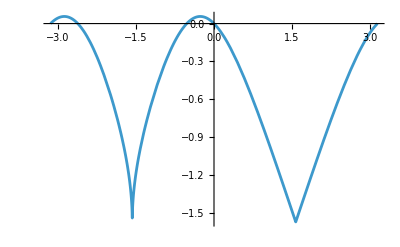

```mathematica
Plot[ArcSin[Sin[a]-√2 Sin[a] √(1+Sin[a])],{a,- π, π}]
```